# Числено диференциране

## Задача: x 0.1^(i = 0) 0.2^(i = 1) 0.3^(i = 2) 0.4^(i = 3) 0.5^(i = 4) -> h = 0.1 y -4 ?(-1) 1 11 20 y' 35 25 60 95 85 y'' X -100 800 -100 X Изп. формули (на листа): 3,4,5,6 y_1 = ? y_0' = (-3 y_0 + 4 y_1 - y_2)/(2h) |.2h y_1 = 1/4(2h*y_0' + 3y_0 + y_2) y_1 = 1/4(2*0.1*35 + 3*(-4) + 1) = -1 y_1' = (y_2 - y_0)/(2h) = (1 -(-4))/(2 * 0.1) = 5/0.2 = 25 y_2' = (y_3 - y_1)/(2h) = (11 - (-1))/(2 * 0.1) = 12/0.2 = 60 y_3' = (y_4 - y_2)/(2h) = (20 - 1)/(2 * 0.1) = 19/0.2 = 95 y_4' = (y_2 - 4 y_3 + 3 y_4)/(2h) = (1 - 4*11 + 3*20)/(2*0.1) = 17/0.2 = 95 y_1'' = (y_0 - 2 y_1 + y_2)/h^2 = (-4 + 2 +1)/0.01 = -1/0.01 = -100 y_2'' = (y_1 - 2 y_2 + y_3)/h^2 = (-1 - 2 + 11)/0.01 = 8/0.01 = 800 y_3'' = (y_2 - 2 y_3 + y_4)/h^2 =(1 - 22 + 20)/0.01 = -1/0.01 = -100

Задача:
x_i = 4 + i*0.1, i = OverBar[0,10]
f(x) = 2sin(x+3)
y_i = f(x_i), i = OverBar[0,10]

```mathematica
xt = Table[4 + i *0.1, {i, 0,10}];
```

```mathematica
f[x_] := 2Sin[x+3]
yt = f[xt]
```

{1.31397,1.45794,1.58734,1.70087,1.79742,1.876,1.93584,1.97634,1.99709,1.99788,1.97872}

```mathematica
h = 0.1
```

0.1

```mathematica
n = Length[xt]
```

11

## Формули с точност O(h) - първи порядък

### Първа производна

```mathematica
yp1 = Table[(yt[[i+1]] - yt[[i]])/h, {i, 1, n - 1}]
```

{1.43965,1.29398,1.13538,0.96543,0.785838,0.598394,0.404971,0.207502,0.00795993,-0.191662}

```mathematica
AppendTo[yp1, (yt[[n]] - yt[[n-1]])/h]
```

{1.43965,1.29398,1.13538,0.96543,0.785838,0.598394,0.404971,0.207502,0.00795993,-0.191662,-0.191662}

{{4.,1.43965},{4.1,1.29398},{4.2,1.13538},{4.3,0.96543},{4.4,0.785838},{4.5,0.598394},{4.6,0.404971},{4.7,0.207502},{4.8,0.00795993},{4.9,-0.191662}}

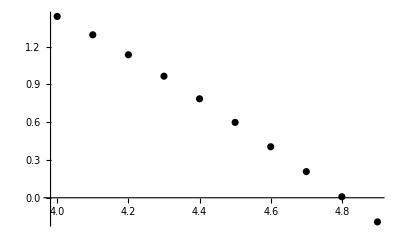

```mathematica
pointsyp1 = Table[{xt[[i]], yp1[[i]]}, {i , 1, n-1}] 
gryp1 = ListPlot[pointsyp1, PlotStyle->Black]
```

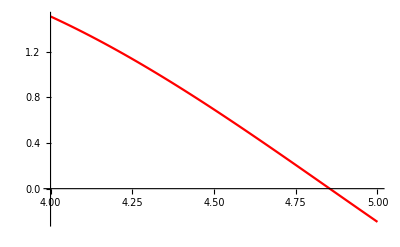

```mathematica
grfyp = Plot[f'[x], {x, xt[[1]], xt[[n]]}, PlotStyle->Red]
```

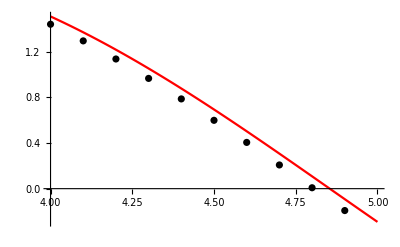

```mathematica
Show[grfyp, gryp1]
```

## Формули с точност O(h^2) - втори порядък

### Първа производна

Попълваме средните точки

```mathematica
yp2 = Table[(yt[[i+1]] - yt[[i-1]])/(2h), {i, 2, n - 1}]
```

{1.36681,1.21468,1.0504,0.875634,0.692116,0.501683,0.306237,0.107731,-0.091851}

Допълваме производната в десния край (последната)

```mathematica
AppendTo[yp2, (yt[[n - 2]] - 4yt[[n-1]] + 3yt[[n]])/(2h)]
```

{1.36681,1.21468,1.0504,0.875634,0.692116,0.501683,0.306237,0.107731,-0.091851,-0.291473}

Допълваме производната в левия край (първата)

```mathematica
PrependTo[yp2, (-3yt[[1]] +4yt[[2]] - yt[[3]])/(2h)]
```

{1.51249,1.36681,1.21468,1.0504,0.875634,0.692116,0.501683,0.306237,0.107731,-0.091851,-0.291473}

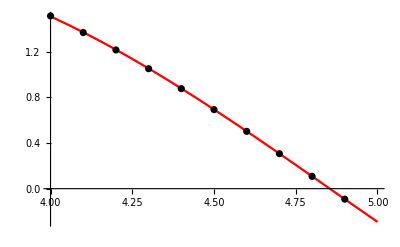

```mathematica
pointsyp2 = Table[{xt[[i]], yp2[[i]]}, {i , 1, n-1}] ;
gryp2 = ListPlot[pointsyp2, PlotStyle->Black];
grfyp = Plot[f'[x], {x, xt[[1]], xt[[n]]}, PlotStyle->Red];
Show[grfyp, gryp2]
```

### Втора производна

Попълваме средните точки

```mathematica
ypp2 = Table[(yt[[i+1]] -2 yt[[i]]+yt[[i-1]])/h^2, {i, 2, n - 1}]
```

{-1.45672,-1.58601,-1.69946,-1.79592,-1.87444,-1.93423,-1.97469,-1.99542,-1.99622}

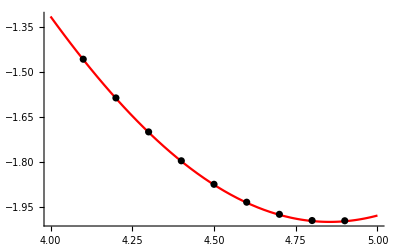

```mathematica
pointsypp2 = Table[{xt[[i + 1]], ypp2[[i]]}, {i , 1, n-2}] ;
grypp2 = ListPlot[pointsypp2, PlotStyle->Black];
grfypp = Plot[f''[x], {x, xt[[1]], xt[[n]]}, PlotStyle->Red];
Show[grfypp, grypp2]
```

# Числено диференциране - повишаване на точността чрез сгъстяване на мрежата

```mathematica
xt = Table[4 + i *0.01, {i, 0,100}];
```

```mathematica
f[x_] := 2Sin[x+3]
yt = f[xt]
```

{1.31397,1.32899,1.34386,1.35861,1.37322,1.38769,1.40202,1.41622,1.43027,1.44417,1.45794,1.47156,1.48503,1.49835,1.51152,1.52454,1.53741,1.55013,1.56269,1.57509,1.58734,1.59942,1.61135,1.62312,1.63472,1.64616,1.65744,1.66855,1.67949,1.69027,1.70087,1.71131,1.72157,1.73167,1.74159,1.75133,1.7609,1.7703,1.77952,1.78856,1.79742,1.8061,1.8146,1.82292,1.83105,1.83901,1.84678,1.85436,1.86176,1.86897,1.876,1.88284,1.88949,1.89595,1.90222,1.9083,1.9142,1.91989,1.9254,1.93072,1.93584,1.94077,1.9455,1.95004,1.95439,1.95854,1.96249,1.96625,1.96981,1.97317,1.97634,1.97931,1.98208,1.98465,1.98702,1.9892,1.99117,1.99295,1.99453,1.99591,1.99709,1.99807,1.99885,1.99942,1.9998,1.99998,1.99996,1.99974,1.99932,1.9987,1.99788,1.99686,1.99564,1.99422,1.99261,1.99079,1.98877,1.98655,1.98414,1.98153,1.97872}

```mathematica
h = 0.01
```

0.01

```mathematica
n = Length[xt]
```

101

## Формули с точност O(h) - първи порядък

### Първа производна

```mathematica
yp1 = Table[(yt[[i+1]] - yt[[i]])/h, {i, 1, n - 1}]
```

{1.50121,1.48792,1.47448,1.4609,1.44716,1.43329,1.41927,1.4051,1.3908,1.37636,1.36178,1.34707,1.33222,1.31723,1.30212,1.28687,1.2715,1.256,1.24037,1.22462,1.20875,1.19275,1.17664,1.16041,1.14406,1.1276,1.11102,1.09434,1.07754,1.06064,1.04363,1.02652,1.0093,0.991988,0.974572,0.957059,0.93945,0.921747,0.903952,0.886067,0.868093,0.850032,0.831886,0.813657,0.795347,0.776957,0.758489,0.739946,0.721329,0.702639,0.683879,0.665051,0.646156,0.627197,0.608175,0.589092,0.56995,0.550751,0.531497,0.51219,0.492832,0.473425,0.45397,0.43447,0.414926,0.395341,0.375716,0.356054,0.336356,0.316624,0.296861,0.277068,0.257248,0.237401,0.217531,0.197639,0.177728,0.157798,0.137853,0.117894,0.0979237,0.0779432,0.0579549,0.0379608,0.017963,-0.00203672,-0.0220362,-0.0420335,-0.0620265,-0.0820134,-0.101992,-0.121961,-0.141917,-0.161859,-0.181785,-0.201692,-0.22158,-0.241445,-0.261287,-0.281102}

```mathematica
AppendTo[yp1, (yt[[n]] - yt[[n-1]])/h]
```

{1.50121,1.48792,1.47448,1.4609,1.44716,1.43329,1.41927,1.4051,1.3908,1.37636,1.36178,1.34707,1.33222,1.31723,1.30212,1.28687,1.2715,1.256,1.24037,1.22462,1.20875,1.19275,1.17664,1.16041,1.14406,1.1276,1.11102,1.09434,1.07754,1.06064,1.04363,1.02652,1.0093,0.991988,0.974572,0.957059,0.93945,0.921747,0.903952,0.886067,0.868093,0.850032,0.831886,0.813657,0.795347,0.776957,0.758489,0.739946,0.721329,0.702639,0.683879,0.665051,0.646156,0.627197,0.608175,0.589092,0.56995,0.550751,0.531497,0.51219,0.492832,0.473425,0.45397,0.43447,0.414926,0.395341,0.375716,0.356054,0.336356,0.316624,0.296861,0.277068,0.257248,0.237401,0.217531,0.197639,0.177728,0.157798,0.137853,0.117894,0.0979237,0.0779432,0.0579549,0.0379608,0.017963,-0.00203672,-0.0220362,-0.0420335,-0.0620265,-0.0820134,-0.101992,-0.121961,-0.141917,-0.161859,-0.181785,-0.201692,-0.22158,-0.241445,-0.261287,-0.281102,-0.281102}

{{4.,1.50121},{4.01,1.48792},{4.02,1.47448},{4.03,1.4609},{4.04,1.44716},{4.05,1.43329},{4.06,1.41927},{4.07,1.4051},{4.08,1.3908},{4.09,1.37636},{4.1,1.36178},{4.11,1.34707},{4.12,1.33222},{4.13,1.31723},{4.14,1.30212},{4.15,1.28687},{4.16,1.2715},{4.17,1.256},{4.18,1.24037},{4.19,1.22462},{4.2,1.20875},{4.21,1.19275},{4.22,1.17664},{4.23,1.16041},{4.24,1.14406},{4.25,1.1276},{4.26,1.11102},{4.27,1.09434},{4.28,1.07754},{4.29,1.06064},{4.3,1.04363},{4.31,1.02652},{4.32,1.0093},{4.33,0.991988},{4.34,0.974572},{4.35,0.957059},{4.36,0.93945},{4.37,0.921747},{4.38,0.903952},{4.39,0.886067},{4.4,0.868093},{4.41,0.850032},{4.42,0.831886},{4.43,0.813657},{4.44,0.795347},{4.45,0.776957},{4.46,0.758489},{4.47,0.739946},{4.48,0.721329},{4.49,0.702639},{4.5,0.683879},{4.51,0.665051},{4.52,0.646156},{4.53,0.627197},{4.54,0.608175},{4.55,0.589092},{4.56,0.56995},{4.57,0.550751},{4.58,0.531497},{4.59,0.51219},{4.6,0.492832},{4.61,0.473425},{4.62,0.45397},{4.63,0.43447},{4.64,0.414926},{4.65,0.395341},{4.66,0.375716},{4.67,0.356054},{4.68,0.336356},{4.69,0.316624},{4.7,0.296861},{4.71,0.277068},{4.72,0.257248},{4.73,0.237401},{4.74,0.217531},{4.75,0.197639},{4.76,0.177728},{4.77,0.157798},{4.78,0.137853},{4.79,0.117894},{4.8,0.0979237},{4.81,0.0779432},{4.82,0.0579549},{4.83,0.0379608},{4.84,0.017963},{4.85,-0.00203672},{4.86,-0.0220362},{4.87,-0.0420335},{4.88,-0.0620265},{4.89,-0.0820134},{4.9,-0.101992},{4.91,-0.121961},{4.92,-0.141917},{4.93,-0.161859},{4.94,-0.181785},{4.95,-0.201692},{4.96,-0.22158},{4.97,-0.241445},{4.98,-0.261287},{4.99,-0.281102}}

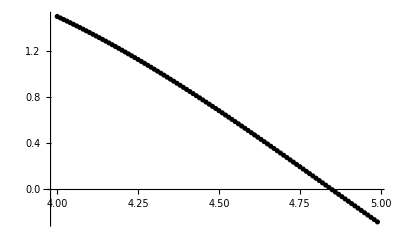

```mathematica
pointsyp1 = Table[{xt[[i]], yp1[[i]]}, {i , 1, n-1}] 
gryp1 = ListPlot[pointsyp1, PlotStyle->Black]
```

```mathematica
grfyp = Plot[f'[x], {x, xt[[1]], xt[[n]]}, PlotStyle->Red]
```

-Graphics-

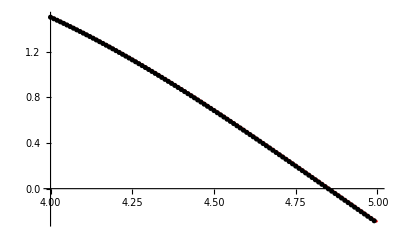

```mathematica
Show[grfyp, gryp1]
```

## Формули с точност O(h^2) - втори порядък

### Първа производна

Попълваме средните точки

```mathematica
yp2 = Table[(yt[[i+1]] - yt[[i-1]])/(2h), {i, 2, n - 1}]
```

{1.49456,1.4812,1.46769,1.45403,1.44022,1.42628,1.41219,1.39795,1.38358,1.36907,1.35442,1.33964,1.32472,1.30967,1.29449,1.27918,1.26375,1.24818,1.23249,1.21668,1.20075,1.18469,1.16852,1.15223,1.13583,1.11931,1.10268,1.08594,1.06909,1.05214,1.03508,1.01791,1.00065,0.98328,0.965816,0.948255,0.930599,0.91285,0.89501,0.87708,0.859063,0.840959,0.822772,0.804502,0.786152,0.767723,0.749218,0.730637,0.711984,0.693259,0.674465,0.655604,0.636677,0.617686,0.598633,0.579521,0.560351,0.541124,0.521844,0.502511,0.483128,0.463697,0.44422,0.424698,0.405133,0.385528,0.365885,0.346205,0.32649,0.306743,0.286965,0.267158,0.247324,0.227466,0.207585,0.187684,0.167763,0.147826,0.127874,0.107909,0.0879334,0.0679491,0.0479579,0.0279619,0.00796311,-0.0120365,-0.0320348,-0.05203,-0.07202,-0.0920027,-0.111976,-0.131939,-0.151888,-0.171822,-0.191739,-0.211636,-0.231513,-0.251366,-0.271194}

Допълваме производната в десния край (последната)

```mathematica
AppendTo[yp2, (yt[[n - 2]] - 4yt[[n-1]] + 3yt[[n]])/(2h)]
```

{1.49456,1.4812,1.46769,1.45403,1.44022,1.42628,1.41219,1.39795,1.38358,1.36907,1.35442,1.33964,1.32472,1.30967,1.29449,1.27918,1.26375,1.24818,1.23249,1.21668,1.20075,1.18469,1.16852,1.15223,1.13583,1.11931,1.10268,1.08594,1.06909,1.05214,1.03508,1.01791,1.00065,0.98328,0.965816,0.948255,0.930599,0.91285,0.89501,0.87708,0.859063,0.840959,0.822772,0.804502,0.786152,0.767723,0.749218,0.730637,0.711984,0.693259,0.674465,0.655604,0.636677,0.617686,0.598633,0.579521,0.560351,0.541124,0.521844,0.502511,0.483128,0.463697,0.44422,0.424698,0.405133,0.385528,0.365885,0.346205,0.32649,0.306743,0.286965,0.267158,0.247324,0.227466,0.207585,0.187684,0.167763,0.147826,0.127874,0.107909,0.0879334,0.0679491,0.0479579,0.0279619,0.00796311,-0.0120365,-0.0320348,-0.05203,-0.07202,-0.0920027,-0.111976,-0.131939,-0.151888,-0.171822,-0.191739,-0.211636,-0.231513,-0.251366,-0.271194,-0.291009}

Допълваме производната в левия край (първата)

```mathematica
PrependTo[yp2, (-3yt[[1]] +4yt[[2]] - yt[[3]])/(2h)]
```

{1.50785,1.49456,1.4812,1.46769,1.45403,1.44022,1.42628,1.41219,1.39795,1.38358,1.36907,1.35442,1.33964,1.32472,1.30967,1.29449,1.27918,1.26375,1.24818,1.23249,1.21668,1.20075,1.18469,1.16852,1.15223,1.13583,1.11931,1.10268,1.08594,1.06909,1.05214,1.03508,1.01791,1.00065,0.98328,0.965816,0.948255,0.930599,0.91285,0.89501,0.87708,0.859063,0.840959,0.822772,0.804502,0.786152,0.767723,0.749218,0.730637,0.711984,0.693259,0.674465,0.655604,0.636677,0.617686,0.598633,0.579521,0.560351,0.541124,0.521844,0.502511,0.483128,0.463697,0.44422,0.424698,0.405133,0.385528,0.365885,0.346205,0.32649,0.306743,0.286965,0.267158,0.247324,0.227466,0.207585,0.187684,0.167763,0.147826,0.127874,0.107909,0.0879334,0.0679491,0.0479579,0.0279619,0.00796311,-0.0120365,-0.0320348,-0.05203,-0.07202,-0.0920027,-0.111976,-0.131939,-0.151888,-0.171822,-0.191739,-0.211636,-0.231513,-0.251366,-0.271194,-0.291009}

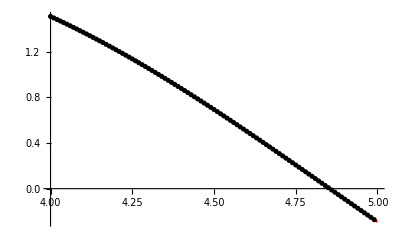

```mathematica
pointsyp2 = Table[{xt[[i]], yp2[[i]]}, {i , 1, n-1}] ;
gryp2 = ListPlot[pointsyp2, PlotStyle->Black];
grfyp = Plot[f'[x], {x, xt[[1]], xt[[n]]}, PlotStyle->Red];
Show[grfyp, gryp2]
```

### Втора производна

Попълваме средните точки

```mathematica
ypp2 = Table[(yt[[i+1]] -2 yt[[i]]+yt[[i-1]])/h^2, {i, 2, n - 1}]
```

{-1.32897,-1.34385,-1.3586,-1.37321,-1.38768,-1.40201,-1.4162,-1.43025,-1.44416,-1.45793,-1.47154,-1.48501,-1.49834,-1.51151,-1.52453,-1.5374,-1.55011,-1.56267,-1.57508,-1.58732,-1.59941,-1.61134,-1.6231,-1.63471,-1.64615,-1.65742,-1.66853,-1.67948,-1.69025,-1.70086,-1.7113,-1.72156,-1.73165,-1.74157,-1.75132,-1.76089,-1.77028,-1.7795,-1.78854,-1.7974,-1.80608,-1.81458,-1.8229,-1.83104,-1.83899,-1.84676,-1.85435,-1.86174,-1.86896,-1.87598,-1.88282,-1.88947,-1.89594,-1.90221,-1.90829,-1.91418,-1.91988,-1.92539,-1.9307,-1.93582,-1.94075,-1.94549,-1.95003,-1.95437,-1.95852,-1.96247,-1.96623,-1.96979,-1.97315,-1.97632,-1.97929,-1.98206,-1.98463,-1.98701,-1.98918,-1.99116,-1.99293,-1.99451,-1.99589,-1.99707,-1.99805,-1.99883,-1.99941,-1.99979,-1.99997,-1.99995,-1.99973,-1.99931,-1.99869,-1.99787,-1.99685,-1.99563,-1.99421,-1.99259,-1.99077,-1.98875,-1.98654,-1.98412,-1.98151}

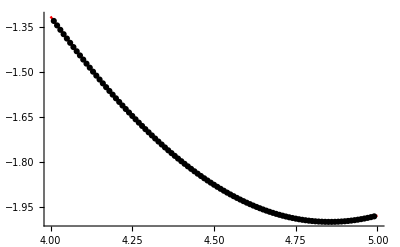

```mathematica
pointsypp2 = Table[{xt[[i + 1]], ypp2[[i]]}, {i , 1, n-2}] ;
grypp2 = ListPlot[pointsypp2, PlotStyle->Black];
grfypp = Plot[f''[x], {x, xt[[1]], xt[[n]]}, PlotStyle->Red];
Show[grfypp, grypp2]
```